```mathematica
(* Set parameters *)
```

```mathematica
taumin=0;
taumax=2.5;
taustep=.5;
kmax=20;
kmin=.1;
pts=12;
logstep=(kmax/kmin)^(1/(pts-1));
```

```mathematica
(* Analytic results and plots *)
```

```mathematica
(* Calculation and ListPlot of the critical points for several values of Tau *)
```

```mathematica
critical={};
Clear[plotkappaC];
plotkappaC=Table[
Subscript[p, k]=UnitStep[k-.5] k^-tau E^(-k/kappa); Subscript[p, k] = Subscript[p, k]/Sum[Subscript[p, k],{k,0,∞}];
(* Definition of the generating functions of the distributions *)
gendeg=GeneratingFunction[Subscript[p, k],k,z]//FullSimplify;  (* degree *)
avg=D[gendeg,z]/.z->1;  (* average degree *)
temp=D[gendeg,z]/avg;  (* excess degree *)
genexc[z_?NumericQ,kappa_]:=temp//FullSimplify;
P[kappa_?NumericQ]:=
1-gendeg/.FindRoot[z-genexc[z,kappa],{z,0.0001,0,1}]//Quiet;

(* calculation of the critical point *)
temp1=D[temp,z]/.z->1;
temp2[kappa_?NumericQ]:=temp1//FullSimplify;
kappaC=kappa/.FindRoot[1==temp2[kappa],{kappa,0.1,0,20}]//Quiet;
Print["τ = ",N[tau,2],"; Critical exp cutoff = ", N[kappaC]];
critical=Append[critical,{tau,kappaC}];

ListLogLinearPlot[{{kappaC,0}},PlotRange->{{kmin,kmax},{0,1}},PlotStyle->Directive[ColorData["DarkRainbow",(taumax-tau)/(taumax-taumin)],PointSize[Large]]]
,{tau,taumin,taumax,taustep}];
```

τ = 0.; Critical exp cutoff = 0.910239

τ = 0.5; Critical exp cutoff = 1.12213

τ = 1.; Critical exp cutoff = 1.4427

τ = 1.5; Critical exp cutoff = 1.97353

τ = 2.; Critical exp cutoff = 2.985

τ = 2.5; Critical exp cutoff = 5.45834

```mathematica
(* Plot of the analytic curve of biggest component size vs exp cutoff *)
```

```mathematica
plots=Table[
Module[{gendeg,avg,genexc,temp,temp1,temp2,k,p},
Subscript[p, k]=UnitStep[k-.5] k^-tau E^(-k/kappa); Subscript[p, k] = Subscript[p, k]/Sum[Subscript[p, k],{k,0,∞}];
(* Definition of the generating functions of the distributions *)
gendeg=GeneratingFunction[Subscript[p, k],k,z]//FullSimplify;  (* degree *)
avg=D[gendeg,z]/.z->1;  (* average degree *)
temp=D[gendeg,z]/avg;  (* excess degree *)
genexc[z_?NumericQ,kappa_]:=temp//FullSimplify;
Print["τ = ",N[tau,2],"; Degree gen func = ", gendeg, "; Exc deg gen func = ", D[gendeg,z]/avg];
P[kappa_?NumericQ]:=
1-gendeg/.FindRoot[z-genexc[z,kappa],{z,0.0001,0,1}]//Quiet;

LogLinearPlot[P[kappa],{kappa,kmin,kmax},PlotRange->{{kmin,kmax},{0,1}},PlotStyle->ColorData["DarkRainbow",(taumax-tau)/(taumax-taumin)]]
]
,{tau,taumin,taumax,taustep}];
```

τ = 0.; Degree gen func = ((-1.+2.71828^(1/kappa)) z)/(2.71828^(1/kappa)-1. z); Exc deg gen func = ((-1.+2.71828^(1/kappa))/(2.71828^(1/kappa)-1. z)+(1. (-1.+2.71828^(1/kappa)) z)/((2.71828^(1/kappa)-1. z)^2))/(1+1./(-1.+2.71828^(1/kappa)))

τ = 0.5; Degree gen func = PolyLog[0.5,ⅇ^(-1./kappa) z]/PolyLog[0.5,ⅇ^(-1./kappa)]; Exc deg gen func = (1. PolyLog[-0.5,ⅇ^(-1./kappa) z])/(z PolyLog[-0.5,ⅇ^(-1./kappa)])

τ = 1.; Degree gen func = Log[1.-1. ⅇ^(-1./kappa) z]/Log[1.-1. ⅇ^(-1./kappa)]; Exc deg gen func = (1. (1.-1. ⅇ^(-1./kappa)))/(1.-1. ⅇ^(-1./kappa) z)

τ = 1.5; Degree gen func = PolyLog[1.5,ⅇ^(-1./kappa) z]/PolyLog[1.5,ⅇ^(-1./kappa)]; Exc deg gen func = (1. PolyLog[0.5,ⅇ^(-1./kappa) z])/(z PolyLog[0.5,ⅇ^(-1./kappa)])

τ = 2.; Degree gen func = PolyLog[2.,ⅇ^(-1./kappa) z]/PolyLog[2.,ⅇ^(-1./kappa)]; Exc deg gen func = (1. Log[1-2.71828^(-1./kappa) z])/(z Log[1-2.71828^(-1./kappa)])

τ = 2.5; Degree gen func = PolyLog[2.5,ⅇ^(-1./kappa) z]/PolyLog[2.5,ⅇ^(-1./kappa)]; Exc deg gen func = (1. PolyLog[1.5,ⅇ^(-1./kappa) z])/(z PolyLog[1.5,ⅇ^(-1./kappa)])

```mathematica
(* Numerical simulations *)
```

```mathematica
(* set number of trials (sample size),
number of nodes in the graph *)
```

```mathematica
trials=100;
n=10000;
cutoff=10^-5;
```

```mathematica
(* Run simulation *)
```

```mathematica
Do[
Print["τ = ", tau];
Clear[data,Z,p];
data={};
Subscript[p, k]=(k+cutoff)^-tau E^(-k/kappa); Z = Integrate[Subscript[p, k],{k,0,∞}];
distrib=ProbabilityDistribution[Subscript[p, k]/Z,{k,0,∞}];
kappa = kmin;
While[kappa≤kmax,
(* Generate a matrix containing degree sequences:
each row corresponds to a specific realization of the 
random degree sequence; there are `trials' rows *)
sequences=
Table[
Module[{sum,degrees},
sum=1;
(* Generate array of degrees; sum must be even *)
While[OddQ[sum],
Clear[degrees];
degrees = Parallelize[Table[

Module[{x, check}, 
check = 0;
While[check != 1,
x = IntegerPart[(-kappa)*Log[1 - RandomReal[]]];
If[RandomReal[] < (x + cutoff)^(-tau), check = 1]
];
x]
(*IntegerPart[RandomVariate[distrib]]*), {i, 1, n}]];
sum=Total[degrees];
];
degrees
],{k,1,trials}];
(* Generate graphs with the specified degree sequences;
g contains all the 'trials' graphs *)
g=Parallelize[Table[RandomGraph[DegreeGraphDistribution[sequences[[i]]]],{i,trials}]];

(* list the size of the largest components of each graph *)
biggest=Table[Length[First[ConnectedComponents[g[[i]]]]]/n,{i,trials}];

(* For each 'kappa' calculate mean and variance of the (relative) size of the largest component
over the 'trials' graphs and store in a table *)
data=Append[data,{N[kappa],N[Mean[biggest]],N[Sqrt[Variance[biggest]/n]]}];

Print["κ = ",N[kappa],"; relative size = ", N[Mean[biggest]], "; Error = ", N[Sqrt[Variance[biggest]/n]]];
kappa*=logstep];

(* Write on file the results: a file for each value of 'tau' *)
Export["~/Codello/graphs/main/output/giant_nodes="<>ToString[IntegerPart[N[n]]]<>"_tau="<>ToString[N[tau,2]]<>".dat",data]

,{tau,taumin,taumax,taustep}]
```

```mathematica
(* Points with errorbars and plots *)
```

```mathematica
Clear[data];
data=Table[
Import["~/Codello/graphs/main/output/giant_nodes="<>ToString[IntegerPart[N[n]]]<>"_tau="<>ToString[N[tau,2]]<>".dat","Table"]
,{tau,taumin,taumax,taustep}];
```

```mathematica
Needs["ErrorBarPlots`"]
Needs["ErrorBarLogPlots`"]
plotanalytic=LogLinearPlot[x,{x,1,30}];
plotpoints=ErrorListLogLinearPlot[data,PlotRange->{{kmin,kmax},{0,1}},PlotStyle->Table[ColorData["DarkRainbow",(taumax-x)/(taumax-taumin)],{x,taumin,taumax,taustep}]];
```

```mathematica
(* Comparison curves and points *)
```

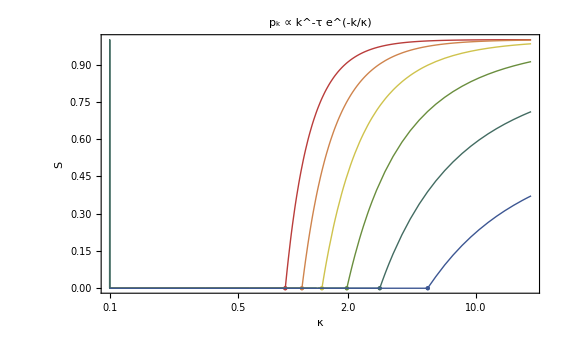

```mathematica
Show[plotkappaC~Join~plots(*~Join~{plotpoints}*), Frame->True,
FrameLabel->{
Style["\!\(\*
StyleBox[κ,\nFontSlant->\"Italic\"]\)",Black,FontSize->12],
Style["\!\(\*
StyleBox[S,\nFontSlant->\"Italic\"]\)",FontSize->12,Black]},
PlotLabel->Style["p_k ∝ k^-τ e^(-k/κ)",Black,FontSize->14],
FrameStyle->Directive[Black,12]
]
```